```mathematica
ClearAll["Global`*"]
```

## V=r^4(2+cos(3θ))

```mathematica
TrigExpand[Cos[3 θ]]
```

Cos[θ]^3-3 Cos[θ] Sin[θ]^2

```mathematica
V[x_,y_]:=(x^2+y^2)^2(2+x^3/((x^2+y^2)^(3/2))-3(x y^2)/((x^2+y^2)^(3/2)))
F[x_,y_]:=-FullSimplify[Grad[V[x,y],{x,y}]]
```

#### Three-direction LLNES

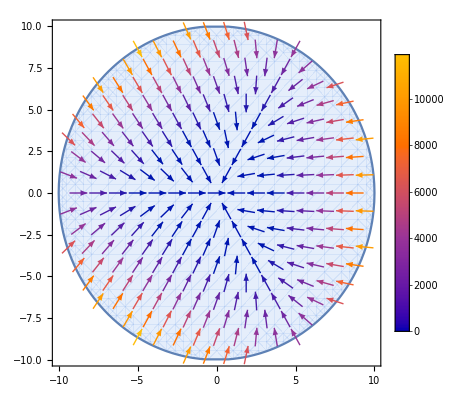

-Graphics-

```mathematica
VectorPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

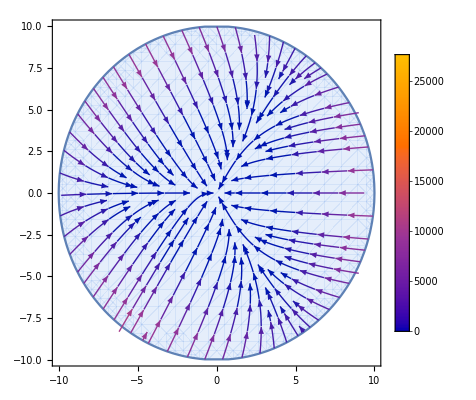

```mathematica
StreamPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

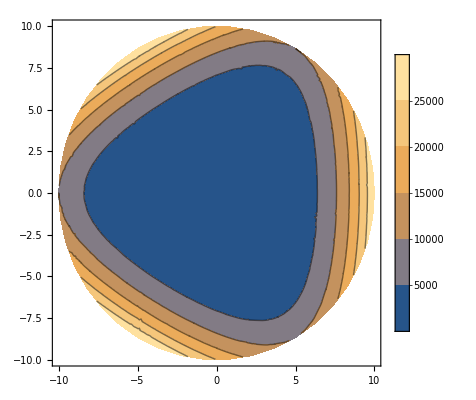

```mathematica
ContourPlot[V[x,y],{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

## V=r^4(2+1/r cos(3θ))

```mathematica
V[x_,y_]:=(x^2+y^2)^2(2+x^3/((x^2+y^2)^(5/2))-3(x y^2)/((x^2+y^2)^(5/2)))
F[x_,y_]:=-FullSimplify[Grad[V[x,y],{x,y}]]
```

#### Radial-symmetry LLNES (the term proportional to r^3 becomes irrelevant)

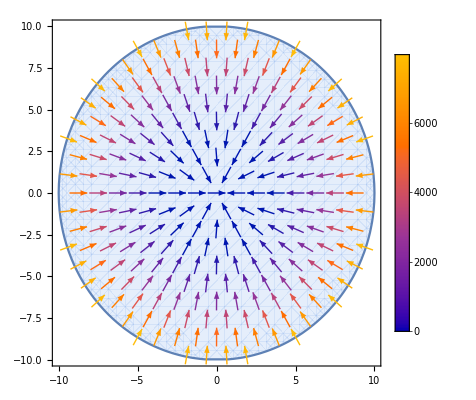

```mathematica
VectorPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

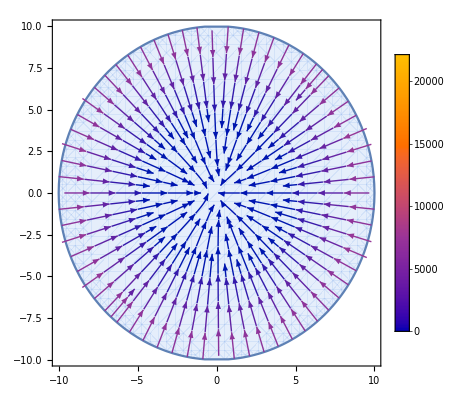

```mathematica
StreamPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

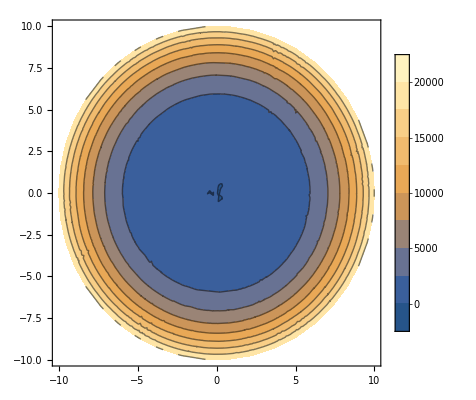

```mathematica
ContourPlot[V[x,y],{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

## V=r^4(2+r cos(3θ))

```mathematica
V[x_,y_]:=(x^2+y^2)^2(2+x^3/((x^2+y^2)^(1/2))-3(x y^2)/((x^2+y^2)^(1/2)))
```

```mathematica
F[x_,y_]:=-FullSimplify[Grad[V[x,y],{x,y}]]
```

#### Saddle point (because the dominant term changes sign with θ, non-confining potential!!)

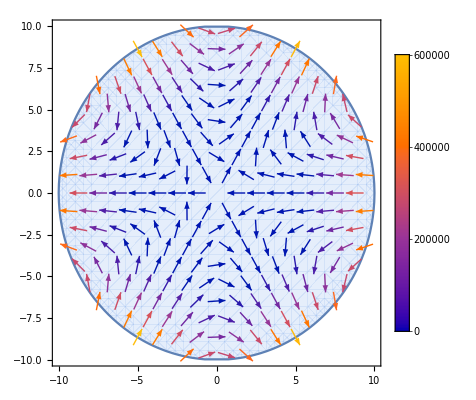

```mathematica
VectorPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

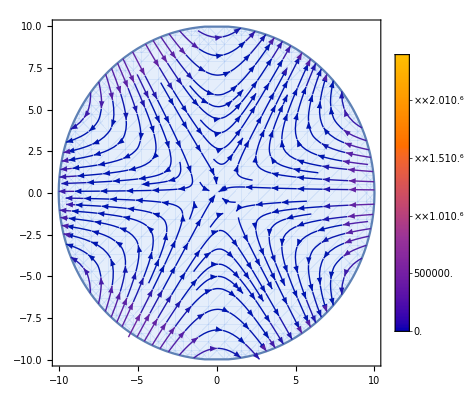

```mathematica
StreamPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

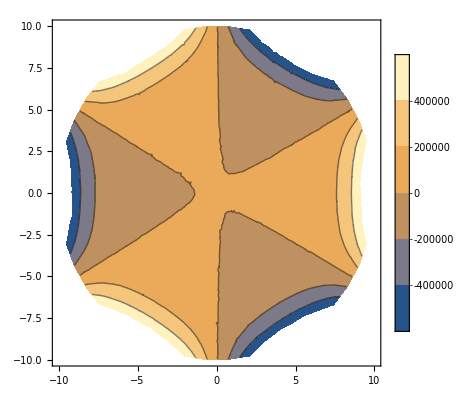

```mathematica
ContourPlot[V[x,y],{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

## V=(x^2+5 y^2)^2

```mathematica
V[x_,y_]:=(x^2+5y^2)^2
F[x_,y_]:=-FullSimplify[Grad[V[x,y],{x,y}]]
```

#### Two-direction LLNES

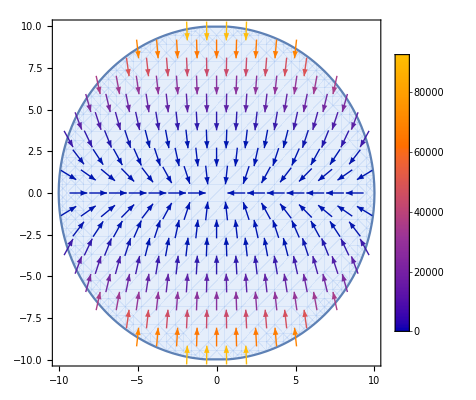

```mathematica
VectorPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

```mathematica
StreamPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],x]
```

StreamPlot::pllim: Range specification {x,y}∈Disk[{0,0},10] is not of the form {x, xmin, xmax}.

StreamPlot[F[u,v]/.{u→x,v→y},{x,y}∈Disk[{0,0},10],x]

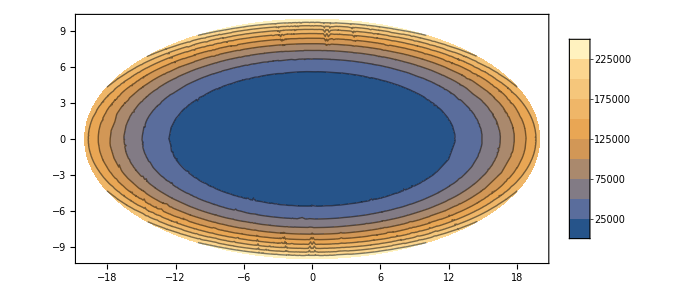

```mathematica
ContourPlot[V[x,y],{x,y}∈Disk[{0,0},{20,10}],PlotLegends->Automatic,AspectRatio->0.5,ImageSize->Large]
```

## V=(x^2+y^2)^2

```mathematica
V[x_,y_]:=(x^2+y^2)^2
```

```mathematica
F[x_,y_]:=-FullSimplify[Grad[V[x,y],{x,y}]]
```

#### Radial-symmetry LLNES

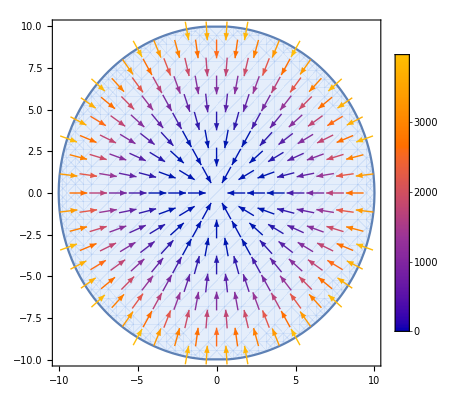

```mathematica
VectorPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

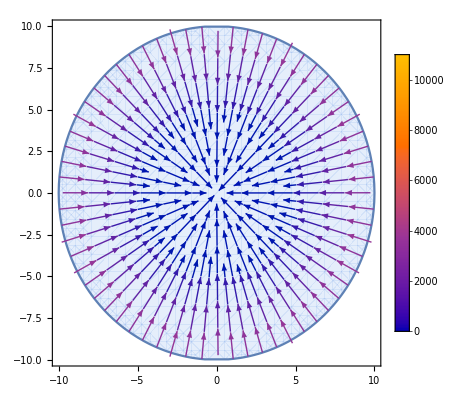

```mathematica
StreamPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

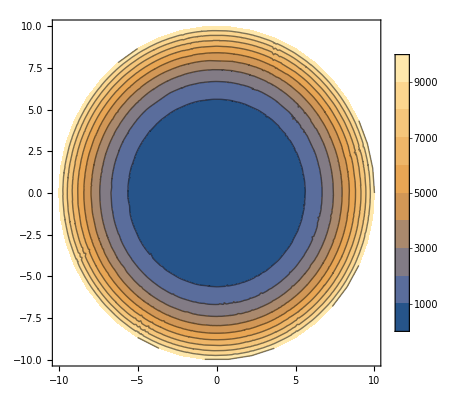

```mathematica
ContourPlot[V[x,y],{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

## V=(x^4+y^4)

```mathematica
V[x_,y_]:=(x^4+y^4)
```

```mathematica
F[x_,y_]:=-FullSimplify[Grad[V[x,y],{x,y}]]
```

#### Four-direction LLNES

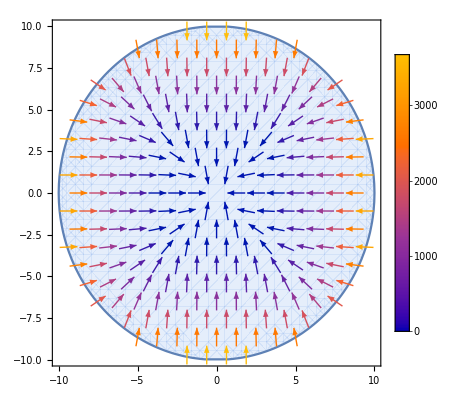

```mathematica
VectorPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

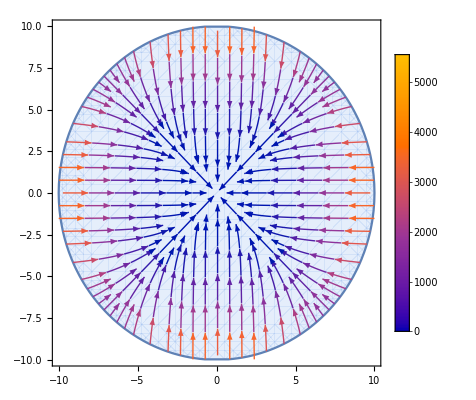

```mathematica
StreamPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

```mathematica
ContourPlot[V[x,y],{x,y}∈Disk[{0,0},10]],PlotLegends->Automatic
```

## V=-r^2+r^4(2+cos(4θ))

```mathematica
TrigExpand[Cos[4 θ]]
```

Cos[θ]^4-6 Cos[θ]^2 Sin[θ]^2+Sin[θ]^4

```mathematica
V[x_,y_]:=-(x^2+y^2)+(x^2+y^2)^2(2+(x^4/((x^2+y^2)^2)-6(x^2 y^2)/((x^2+y^2)^2)+y^4/((x^2+y^2)^2)))
```

```mathematica
F[x_,y_]:=-FullSimplify[Grad[V[x,y],{x,y}]]
```

#### Four-direction LLNES

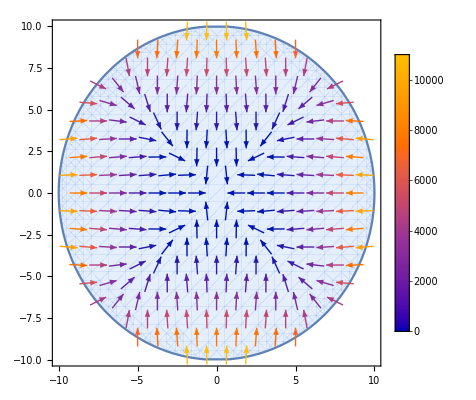

```mathematica
VectorPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

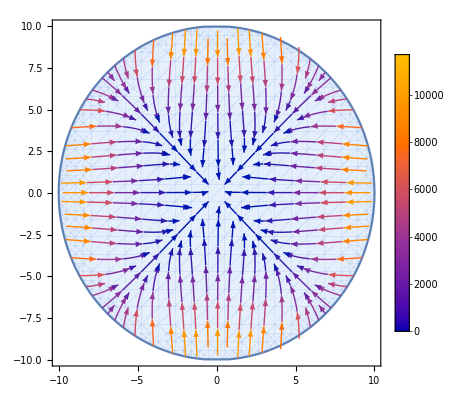

```mathematica
StreamPlot[F[u,v]/.{u->x,v->y},{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

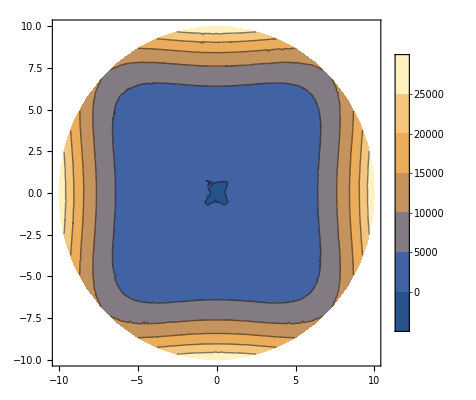

```mathematica
ContourPlot[V[x,y],{x,y}∈Disk[{0,0},10],PlotLegends->Automatic]
```

## V = (x^2 + y^2 + 4 z^2)^2

```mathematica
V[x_,y_,z_]:=(x^2+y^2+3z^2)^2 /4
F[x_,y_,z_]:=-Grad[V[x,y,z],{x,y,z}]
```

#### 3d LLNES

```mathematica
StreamPlot3D[F[x,y,z],{x,y,z}∈Ellipsoid[{0,0,0},{10,10,5}],BoxRatios->{10,10,5},ImageSize->Medium,StreamMarkers->"Arrow"]
```

-Graphics3D-

## V = (x^2 + 4 y^2 + 10 z^2)^2

```mathematica
V[x_,y_,z_]:=(x^2+4y^2+10z^2)^2
F[x_,y_,z_]:=-Grad[V[x,y,z],{x,y,z}]
```

#### 3d LLNES

```mathematica
StreamPlot3D[F[x,y,z],{x,y,z}∈Ellipsoid[{0,0,0},{10,5,√10}],BoxRatios->{10,5,√10},ImageSize->Medium,StreamMarkers->"Arrow"]
```

-Graphics3D-